# Bifurcation Diagrams

-Bifurcation analysis on a, attack rate by animals on plant rewards, interpreted as foraging efficiency
-Using Main-Text Models and notation following Hale et al. 2021
-Curves were assessed for stability and colored manually in Adobe Illustrator, green or black for plant or animal equilibrium density (top or bottom panels), respectively
-Solutions for one species that are infeasible for the other were excluded

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

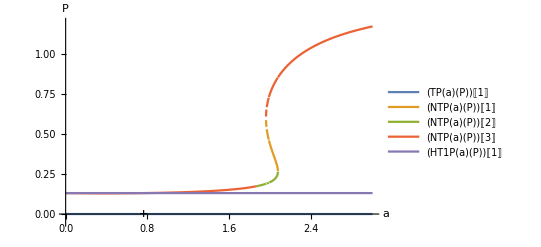

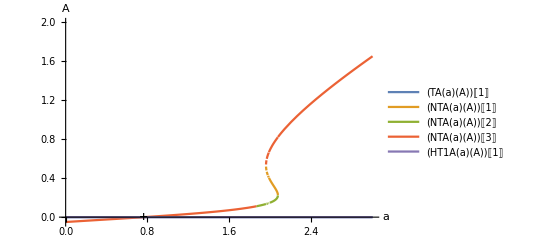

```mathematica
(* Pollination *) 
(* parameters *) 
bP=1.5; f = 0.5; φ=0.5; g=1;sP=0.61; dP=0.67; 
h=0.01;
bA=1; ε=1; sA=2; dA=1.1;

rP = bP*f*g-dP; rPmax = rP+bP*φ*g;
rA = bA-dA;

condition = (-rA*sP)/(rP* (ε+h*rA));

(* non-trivial equilibrium *) 
equilibriaNT = Solve[{bP*(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP==0, bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* trivial equilibrium *) 
equilibriaT=Solve[{P==0, A==0},{P,A}];

(* half-trivial equilibria *)
equilibriaHT1=Solve[{bP*(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP==0, A==0},{P,A}];
equilibriaHT2=Solve[{P==0,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* expressions for equilibria as a function of a and species density (P, A) *)
NTP[a_][P_] := Evaluate[P /. equilibriaNT]
NTA[a_][A_] := Evaluate[A /. equilibriaNT]
TP[a_][P_] := Evaluate[P /. equilibriaT]
TA[a_][A_] := Evaluate[A /. equilibriaT]
HT1P[a_][P_] := Evaluate[P /. equilibriaHT1]
HT1A[a_][A_] := Evaluate[A /. equilibriaHT1]
HT2P[a_][P_] := Evaluate[P /. equilibriaHT2]
HT2A[a_][A_] := Evaluate[A /. equilibriaHT2]

(* plotting the bifurcation diagrams, using different colors for the different equilibria, so it's easy to see transitions in dynamics *) 
(* not automatically calculating if they are stable or not--too computationally intensive *)

(* plant equilibrium density *)
Show[Plot[{TP[a][P][[1]],NTP[a][P][[1]],NTP[a][P][[2]],NTP[a][P][[3]],HT1P[a][P][[1]]},{a,0,3},PlotLegends->"Expressions",PlotRange->{-0.05,1.2}],ListPlot[{{condition,0}},PlotMarkers->{"+"},PlotStyle->Black],AxesLabel->{a,P}]

(* animal equilibrium density *)
Show[Plot[{TA[a][A][[1]],NTA[a][A][[1]],NTA[a][A][[2]],NTA[a][A][[3]],HT1A[a][A][[1]]},{a,0,3},PlotLegends->"Expressions",PlotRange->{-0.05,2}],ListPlot[{{condition,0}},PlotMarkers->{"+"},PlotStyle->Black],AxesLabel->{a,A}]
```

-4.

0.5

0.0227273

1.33333

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

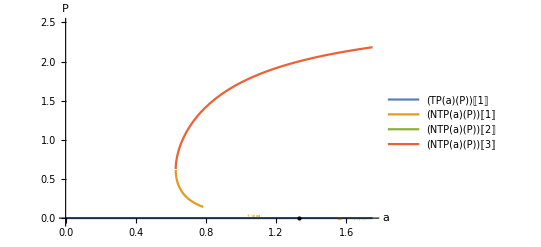

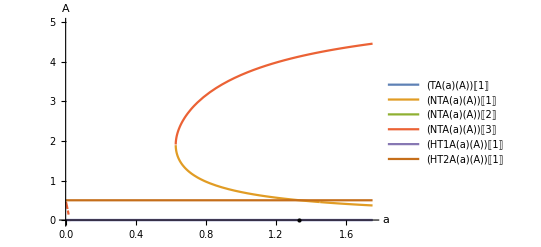

```mathematica
(* Germination *) 
(* parameters *) 
bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.7; 
rP = bP*f*g-dP; rPmax = rP+bP*f*γ;
rP/sP
h=1;

bA=1; ε=1; sA=0.2; dA=0.9;
rA = bA-dA;
rA/sA

condition1 = (-rA*sP)/(rP* (ε+h*rA))
condition2 = (-rP*sA)/(rPmax * rA)

(* non-trivial equilibrium *) 
equilibriaNT = Solve[{bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP==0,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* trivial equilibrium *) 
equilibriaT=Solve[{P==0, A==0},{P,A}];

(* half-trivial equilibria *)
equilibriaHT1=Solve[{bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP==0, A==0},{P,A}];
equilibriaHT2=Solve[{P==0, bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* expressions for equilibria as a function of a and species density (P, A) *)
NTP[a_][P_] := Evaluate[P /. equilibriaNT]
NTA[a_][A_] := Evaluate[A /. equilibriaNT]
TP[a_][P_] := Evaluate[P /. equilibriaT]
TA[a_][A_] := Evaluate[A /. equilibriaT]

HT1P[a_][P_] := Evaluate[P /. equilibriaHT1]
HT1A[a_][A_] := Evaluate[A /. equilibriaHT1]
HT2P[a_][P_] := Evaluate[P /. equilibriaHT2]
HT2A[a_][A_] := Evaluate[A /. equilibriaHT2]

(* plant equilibrium density *)
Show[Plot[{TP[a][P][[1]],NTP[a][P][[1]],NTP[a][P][[2]],NTP[a][P][[3]]},{a,0,1.75},PlotLegends->"Expressions",PlotRange->{-0.05,2.5}],Graphics[Point[{condition2,0}]],AxesLabel->{a,P}]

(* animal equilibrium density *)
Show[Plot[{TA[a][A][[1]],NTA[a][A][[1]],NTA[a][A][[2]],NTA[a][A][[3]],HT1A[a][A][[1]],HT2A[a][A][[1]]},{a,0,1.75},PlotLegends->"Expressions",PlotRange->{-0.05,5}],Graphics[Point[{condition2,0}]],AxesLabel->{a,A}]
```

0.15

-1

-12.5

3.10078

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

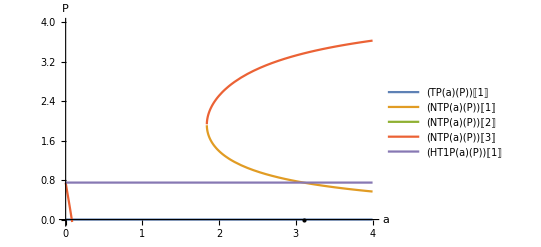

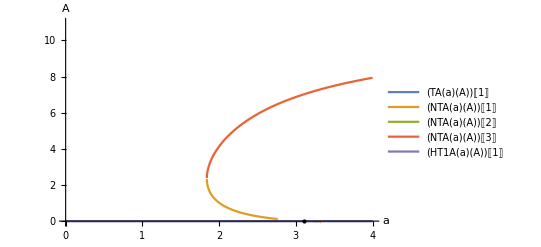

```mathematica
(* Negative Denisty-Dependence *) 
(* parameters *) 
bP=1; f = 1; g=1;sP=0.2; σ =0.2;dP=0.85; 
h=0.5;
bA=1; ε=0.93; sA=0.08; dA=2;

rP = bP*f*g-dP
rA = bA-dA
rA/sA

condition1 = (-rA*sP)/(rP* (ε+h*rA))

(* non-trivial equilibrium *) 
equilibriaNT = Solve[{bP*f*g-(sP-σ*(a*A)/(1+a*h*P+a*A))*P-dP==0 ,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* trivial equilibrium *) 
equilibriaT=Solve[{P==0, A==0},{P,A}];

(* half-trivial equilibria *)
equilibriaHT1=Solve[{bP*f*g-(sP-σ*(a*A)/(1+a*h*P+a*A))*P-dP==0 , A==0},{P,A}];
equilibriaHT2=Solve[{P==0,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* expressions for equilibria as a function of a and species density (P, A) *)
NTP[a_][P_] := Evaluate[P /. equilibriaNT]
NTA[a_][A_] := Evaluate[A /. equilibriaNT]
TP[a_][P_] := Evaluate[P /. equilibriaT]
TA[a_][A_] := Evaluate[A /. equilibriaT]

HT1P[a_][P_] := Evaluate[P /. equilibriaHT1]
HT1A[a_][A_] := Evaluate[A /. equilibriaHT1]
HT2P[a_][P_] := Evaluate[P /. equilibriaHT2]
HT2A[a_][A_] := Evaluate[A /. equilibriaHT2]

(* plant equilibrium density *)
Show[Plot[{TP[a][P][[1]],NTP[a][P][[1]],NTP[a][P][[2]],NTP[a][P][[3]],HT1P[a][P][[1]]},{a,0,4},PlotLegends->"Expressions",PlotRange->{-0.05,4}],Graphics[Point[{condition1,0}]],AxesLabel->{a,P}]

(* animal equilibrium density *)
Show[Plot[{TA[a][A][[1]],NTA[a][A][[1]],NTA[a][A][[2]],NTA[a][A][[3]],HT1A[a][A][[1]]},{a,0,4},PlotLegends->"Expressions",PlotRange->{-0.05,11}],Graphics[Point[{condition1,0}]],AxesLabel->{a,A}]
```